Solving an SVM by hand based on KKT conditions
by Forrest Sheng Bao at Iowa State University
Copyleft 2020

Although necessary but not sufficient, the KKT conditions are sufficient for optimality if the problem is to minimize a convex function which is the case for an SVM in primal form. Therefore, from KKT conditions alone, we can solve an SVM by hand.

Solving a system of equations in Mathematica

```mathematica
Solve[{a1+a2==2, a1-a2==10}, {a1, a2}]
```

{{a1→6,a2→-4}}

Solving a simple SVM of only two samples.

The plot below indicates two two samples, (1,1) of class +1, and (0,0) of class -1. Denote the first one as sample 1 and the second as sample 2. A well-trained SVM would be the one depicted by the blue line.

```mathematica
plt1= ListPlot[{{0,0},{1,1}}, PlotStyle->{AbsolutePointSize[10]}, AspectRatio->1];
plt2 =ListLinePlot[{{0,1},{1,0}}];
Show[plt1, plt2]
```

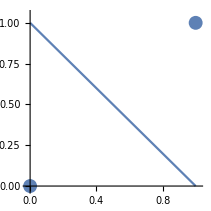

First, using the gradient on the bias term that  ∑_(k=1)^K λ_k yk=0, we have (λ_1 | λ_2)(+1
-1)=0

Then, write one equation for each sample in the complementary slackness equation (Equation D in slides):  λ_1[+1· ((w1 | w2)(1
1)+w_b)-1]=0
λ_2[-1·((w1 | w2)(0
0)+w_b)-1]=0

Finally, the gradient on the non-bias weights:  (w1
w2)=λ_1·(1
1)-λ_2·(0
0)

Expand matrix equations above into a system of linear equations and solve them using the Solve function. For typesetting easiness,  λ’s are replaced with a’s in the code below.

```mathematica
Solve[{ a1-a2== 0,
         a1 *(w1+w2 +wb-1) == 0,
         a2 *(-1*wb-1) == 0,
         w1 ==  a1,
        w2== a1
}, {a1,a2,w1,w2,wb}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a1→0,a2→0},{a1→0,a2→0,wb→-1},{a1→0,a2→0,wb→1},{a1→1,a2→1,wb→-1}}

The first 3 solutions set both a1 and a2 to 0. They should be discarded as they remove the constraints from the Lagrange multiplier. 
The last solution is what we want, demonstration an equation x+y-1=0 which beautifully goes between the two samples at 135 degree. The fact that neither a1 nor a2 are zero indicates that both samples are the supporting vectors.

Let’s see more examples.

```mathematica
Solve[{a1+a2-a3 -a4 == 0,
         a1 *(1*(w1+w2+wb)-1)==0,
         a2*(1*(w1+ 0+  wb)-1)==0,
         a3*(-1*(0  + 0+  wb)-1)==0,
         a4*(-1*(0  + w2+  wb)-1)==0,
         w1 ==  a1 + a2,
         w2 ==  a1 - a4,
a1≥ 0,a2≥0,a3≥ 0, a4≥0
}, {w1,w2,a1,a2,a3,a4,wb}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a1→0,a2→0,a3→0,a4→0},{a1→1,a2→0,a3→1,a4→0,wb→-1}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a1→0,a2→0},{a1→0,a2→0,wb→-1},{a1→0,a2→0,wb→1},{a1→1,a2→1,wb→-1}}

```mathematica
Solve[{a1-a2-a3 +a4 == 0,
         a1 *(1*(w1+w2+wb)-1)==0,
         a2*(-1*(w1+ 0+  wb)-1)==0,
         a3*(-1*(0  + 0+  wb)-1)==0,
         a4*(1*(0  + w2+  wb)-1)==0,
         w1 ==  a1 - a2,
         w2 ==  a1 + a4,
a1≥ 0,a2≥0,a3≥ 0, a4≥0
}, {w1,w2,a1,a2,a3,a4,wb}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a1→0,a2→0,a3→0,a4→0},{a1→1,a2→0,a3→1,a4→0,wb→-1}}

Get::noopen: Cannot open CloudObjectLoader`.